Lab 4: Gamma, Beta, and Alpha Particle Attenuation
J.R. Powers - Luhn
09 February 2017
Thursday
Lab Partner: Dory Miller

Pre-Laboratory Questions:

1. How long does it take for Y-90 to become in secular equilibrium with Sr-90? What is the ratio of their activities?

```mathematica
(* half life of Y-90 64.1h *)
Y90HalfLife=64.1;
(* half life of Sr-90 28.79y *)
Sr90HalfLife=28.79*365.241*24; (*convert to hours*)
8*Y90HalfLife
```

512.8

The two isotopes reach secular equilibrium in 8 half-lives of the daughter nuclide, t_(1/2)=512.8h . At this point their activities are equal, A_(Sr-90)=A_(Y-90)

2. Using the NIST ESTAR database, determine the range of the most probable and maximum emission energy for the beta particles from Sr-90 and Y-90 in Aluminum and plastic. Provide the answer in units of mass thickness (mg/cm^2).

```mathematica
(* From https://www.nndc.bnl.gov/chart/decaysearchdirect.jsp?nuc=90SR&unc=nds *)
Sr90BetaEnergy={195.88} (* keV *);
(* From https://www.nndc.bnl.gov/chart/decaysearchdirect.jsp?nuc=90Y&unc=nds *)
Y90BetaEnergy={25.07,185.61,933.7} (* keV *);
```

```mathematica
(* Ranges in Aluminum *)
{{Beta Energy
(keV), Stopping Power
(cm^2/g), Range
(mg/cm^2)}, {195.8, 2.204, 88.84}, {25.07, 8.328, 3.010}, {185.61, 2.261, 82.09}, {933.7, 1.489, 627.1}};
```

```mathematica
(* Ranges in Plastic (Polyethylene) *)
{{Beta Energy
(keV), Stopping Power
(cm^2/g), Range
(mg/cm^2)}, {195.8, 3.001, 29.60}, {25.07, 11.89, 0.2532}, {185.61, 3.081, 26.64}, {933.7, 1.950, 321.6}};
```

The 933.7keV beta is the most probable decay for Y-90; The 195.8keV beta is the most probable decay for Sr-90.

3. Where are gamma rays on the electromagnetic spectrum? What are the characteristics of their wavelength, frequency, and energy?

Gamma rays are the most energetic photons on the electromagnetic spectrum. Their wavelength is on the order of tenths of angstroms (10^-11 m), making their frequency on order of 10^19 Hz. Their energies are normally in the range of tens to hundreds of keV, but can reach the MeV range.

4. Using the NIST X-ray Mass Attenuation Coefficient Database (http://www.nist.gov/pml/data/xraycoef/), use linear interpolation to find the mass attenuation coefficient of 88keV gamma-rays in Aluminum. Provide the answer in units of cm^2/mg.

```mathematica
e0=80 (* keV *);
e1=100 (* keV *);
mu0=0.2018 * 10^-3 (* cm^2/mg *);
mu1=0.1704 * 10^-3 (* cm^2/mg *);
mu=mu0+(mu1-mu0)/(e1-e0)*(88-e0)
```

0.00018924

Mass attenuation coefficient for 88keV gammas in Aluminum is 1.892*10^-4 cm^2/mg.

5. Using the value found in question 4, calculate the thickness of Aluminum required to absorb between 10-80% of the 88keV gamma-rays in steps of 10%.

```mathematica
density=2700 (* mg/cm^3 *);
ap=Table[i,{i,0.1,0.8,0.1}] (* Attenuation Percentages *);
at=Table[-1/(mu*density)*Log[1-ap[[i]]],{i,Length[ap]}]//N;
Multicolumn[Join[ap,at],2]
```

0.1 | 0.206206
0.2 | 0.436725
0.3 | 0.698065
0.4 | 0.99976
0.5 | 1.35659
0.6 | 1.79332
0.7 | 2.35635
0.8 | 3.14991

See above for the thickness (in cm, second column) to attenuate the gamma-rays to the fractions in the first column.

6. Calculate the mass thickness of an aluminum shim 0.080±0.005 inches thick. Report your answer in cm^2/mg.

```mathematica
1/density*1/(0.080*2.54)
1/density*1/(0.080*2.54)^2*0.005*2.54
```

0.00182269

0.000113918

The mass thickness of an aluminum shim is 0.0018±0.00011 cm^2/mg

In-Lab

Beta particle attenuation

1. With no radiation sources around your station, take a background measurement. Use the count time of 60 seconds and 10 runs.

```mathematica
PartABackgroundFilename="beta_bkg.dat";
PartABackgroundCounts=Import[NotebookDirectory[]<>PartABackgroundFilename][[12;;]][[;;,3]]
```

{36,39,36,37,43,32,43,51,40,30}

2. Use a hollow source holder to hold the Sr-90 source up on the second to top shelf. Take a 60 second count. Record actual setup parameters.

3. On the top shelf, place an absorber between the source and the detector. Choose an absorber that is approximately 10% of the range for the maximum emission energy of Sr-90.

4. Repeat step 3 for five more absorbers with mass thicknesses between 30% and 300% the range of the most probable beta energy for Sr-90. Use any material absorbers for these measurements that meet the mass thickness requirements. Record the absorber material, mass thickness and count data for all experiments in your laboratory notebook.

```mathematica
PartASr90DataFilename="beta_exp.dat";
PartASr90Counts=Import[NotebookDirectory[]<>PartASr90DataFilename][[12;;]][[;;,3]]
PartAAbsorberThicknesses={0.,0.,19.2,102,141,216,522,655} (* mg/cm^2 *)
```

{10570,10294,8385,4859,4408,3542,729,295}

{0.,0.,19.2,102,141,216,522,655}

5. Return the beta source to the GTA.

Alpha particle attenuation

1. Measure the distance between the source holder shelves and note it in the laboratory notebook.

```mathematica
ShelfSeparationDistance=0.8 (* cm *);
```

2. Check out a Po-210 source from the GTA. Note the source born date to estimate the source strength.

Po-210 source dated October 2014, 0.1 μCi. t_(1/2)=138.4

3. Place a series of 0.08±0.005 inch aluminum shims on the source holder so that, when the Po-210 alpha source is placed on top, the distance between the alpha source and GM window is minimized but not touching the GM window.

4. Estimate the separation distance between the source and the window of the GM tube.

Separation distance approximately 0.3 cm

5. Conduct one 60 second counting experiment. Record your results in your laboratory notebook.

6. Remove one of the aluminum shims from the source holder and repeat step 5.

7. Repeat step 6 until all but one aluminum shim has been removed. Then move the source holder down one shelf, add shims to get the next separation distance approximately equal to one aluminum shim thickness, and continue taking 60 second counts at each separation distance.

8. When the count rate observed is approximately equal to the background, take a couple more measurements to enhance the fidelity of the collected data for post-lab analysis.

```mathematica
(* All data recorded in single file *)
PartBPo210DataFilename="alpha_exp.dat";
PartBPo210Counts=Import[NotebookDirectory[]<>PartBPo210DataFilename][[12;;]][[;;,3]]
```

{165,101,72,54,30,30,30}

```mathematica
PartBPo210SourceDistance={0.3,0.5,0.7,0.9,1.1,1.3,1.5} (* cm *)
AluminumDensity=2700 (* mg/cm^3 *);
```

{0.3,0.5,0.7,0.9,1.1,1.3,1.5}

9. Return the Po-210 source to the GTA.

Gamma-ray attenuation

NOTE: Data were not collected in lab. Instead, Prof. Lukosi collected data for extended time periods. Error propogation will be conducted assuming that there is no error in the counting time.

1. Check out a 1μCi Cd-109 button source (or other low energy gamma-ray source) from the GTA.

2. Place the source on the source holder on the second shelf of the GM test stand. Place another source holder on the top shelf with one aluminum shim on it and conduct a 60 second count.

3. Now start adding aluminum shims to the top source holder to attenuate some of the 88 keV gamma-rays. Use the answer from the pre-laboratory exercise to attenuate between 10% and 80% of the incident 88 keV gamma-rays. Conduct a total of four experiments between this range at 60 second count times each.

4. Record results in the laboratory notebook (i.e., how many shims used and counts observed for each).

5. Return the Cd-109 button source to the GTA.

Post-Lab

```mathematica
Beta particle attenuation
```

attenuation Beta particle

1. From the data collected in steps 1-4, determine the background and dead time corrected count rate for all data collected and the associated uncertainty.

```mathematica
τ=267*10^-6; (* s, from lab 3 data at station 1. Assume error=0 *)
PartACountTime=60; (* s, Assume error=0 *)
```

```mathematica
PartABackgroundCountRate=Total[PartABackgroundCounts]/600//N
```

0.645

```mathematica
PartABackgroundCountRateError=1/600*√Total[PartABackgroundCounts]//N
```

0.0327872

```mathematica
DeadTimeCorrectedCounts[uncorrected_]:=uncorrected / (1-uncorrected * τ)
```

```mathematica
MyDumbError[u_]=D[DeadTimeCorrectedCounts[u],u]
```

1/(1-(267 u)/1000000)+(267 u)/(1000000 (1-(267 u)/1000000)^2)

```mathematica
PartADeadTimeCorrectedBackgroundRate=DeadTimeCorrectedCounts[PartABackgroundCountRate]
PartADeadTimeCorrectedBackgrounRateError=√(MyDumbError[PartABackgroundCountRate]^2*PartABackgroundCountRateError^2)//N
```

0.645111

0.0327985

```mathematica
PartASr90CountRate=PartASr90Counts/PartACountTime;
PartASr90CountRateErrors=√(PartASr90Counts/PartACountTime^2);
```

```mathematica
PartADeadTimeCorrectedCountRates=DeadTimeCorrectedCounts[PartASr90CountRate]//N
```

{184.862,179.803,145.167,82.7731,74.9366,59.9787,12.1895,4.92313}

```mathematica
PartADeadTimeCorrectedCountRatesError=√(MyDumbError[PartASr90CountRate]^2*PartASr90CountRateErrors^2)//N
```

{1.88683,1.85725,1.64676,1.21369,1.15127,1.02394,0.452934,0.287012}

```mathematica
PartADeadTimeAndBackgroundCorrectedCountRates=PartADeadTimeCorrectedCountRates-PartADeadTimeCorrectedBackgroundRate
PartADeadTimeAndBackgroundCorrectedCountRatesError=√(PartADeadTimeCorrectedCountRatesError^2+PartADeadTimeCorrectedBackgrounRateError^2)
```

{184.217,179.158,144.522,82.128,74.2915,59.3336,11.5444,4.27802}

{1.88712,1.85754,1.64709,1.21414,1.15174,1.02446,0.45412,0.28888}

```mathematica
PartAPlotData=Multicolumn[Join[PartAAbsorberThicknesses,PartADeadTimeAndBackgroundCorrectedCountRates,PartADeadTimeAndBackgroundCorrectedCountRatesError],3]//First
```

{{0.,184.217,1.88712},{0.,179.158,1.85754},{19.2,144.522,1.64709},{102,82.128,1.21414},{141,74.2915,1.15174},{216,59.3336,1.02446},{522,11.5444,0.45412},{655,4.27802,0.28888}}

2. Plot the data from part 1 on a semi-log scale with error bars (i.e., transmitted beta fraction vs. absorber thickness). The slope of this line will be the mass attenuation coefficient.

```mathematica
Needs["ErrorBarLogPlots`"];
```

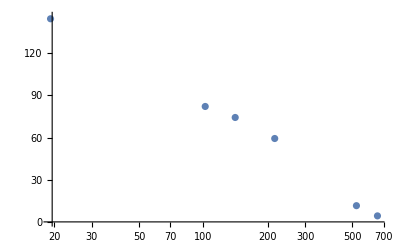

```mathematica
ErrorListLogLinearPlot[PartAPlotData,ErrorBarFunction->ErrorBarScale[1]]
```

3. Using linear regression, find the slope and its uncertainty. Report the value in units of cm^2/mg in a new, text-formatted cell.

```mathematica
PartAFitData=Multicolumn[Join[PartAPlotData[[;;,1]],Log[PartAPlotData[[;;,2]]]],2]//First
Fit[PartAFitData[[;;,1;;2]], {1,t}, t]
```

{{0.,5.21611},{0.,5.18827},{19.2,4.97343},{102,4.40828},{141,4.308},{216,4.08318},{522,2.4462},{655,1.45349}}

5.1349-0.00543875 t

4. Using equation 4, determine the mass attenuation coefficient for Sr-90 and Y-90 in units of cm^2/mg.

Equation Four: μ(E_Max)=1.7*E_Max^-1.14

```mathematica
MassAttenuationCoefficientSr90=1.7*546^-1.14
MassAttenuationCoefficientY90=1.7*2280.1^-1.14
```

0.0012884

0.00025257

5. Comment on how well the collected data agrees with that calculated in equation 4. Include a discussion on the fact that Y-90 is present in the Sr-90 source, and whether this may have affected the experimental result and its comparison with the calculated mass attenuation coefficient.

While the calculated value for Sr-90 is lower (less attenuating) than that determined in the lab, the sample had partially decayed to Y-90, which emits three additional betas at varying energy. The resultant number of counts, therefore, includes all four of these betas. To account for this, a more accurate equation would have been R_T=R_1 ⅇ^-μ_1t+R_2 ⅇ^-μ_2t+R_3 ⅇ^-μ_3t+R_4 ⅇ^-μ_4t.

```mathematica
Alpha particle attenuation
```

Alpha attenuation particle

1. From the data collected, determine the average count rate (background corrected and dead time corrected) with uncertainty, for all shims used.

```mathematica
PartBPo210Counts
```

{165,101,72,54,30,30,30}

```mathematica
PartBPo210CountsError=√PartBPo210Counts//N
```

{12.8452,10.0499,8.48528,7.34847,5.47723,5.47723,5.47723}

```mathematica
PartBCountTime=60; (* s, Assume error=0 *)
```

```mathematica
PartBCountRates=PartBPo210Counts/PartBCountTime//N
```

{2.75,1.68333,1.2,0.9,0.5,0.5,0.5}

```mathematica
PartBCountRateErrors=√(PartBPo210Counts/PartBCountTime^2)//N
```

{0.214087,0.167498,0.141421,0.122474,0.0912871,0.0912871,0.0912871}

```mathematica
PartBDeadTimeCorrectedCountRates=DeadTimeCorrectedCounts[PartBCountRates]
```

{2.75202,1.68409,1.20038,0.900216,0.500067,0.500067,0.500067}

```mathematica
PartBDeadTimeCorrectedCountRateErrors=√(MyDumbError[PartBDeadTimeCorrectedCountRates]^2*PartBCountRateErrors^2)//N
```

{0.214402,0.167649,0.141512,0.122533,0.0913115,0.0913115,0.0913115}

```mathematica
(* Using the background count rate from part A *)
PartBDeadTimeAndBackgroundCorrectedCountRates=PartBDeadTimeCorrectedCountRates-PartADeadTimeCorrectedBackgroundRate
```

{2.10691,1.03898,0.555274,0.255105,-0.145044,-0.145044,-0.145044}

```mathematica
PartBDeadTimeAndBackgroundCorrectedCountRateErrors=√(PartBDeadTimeCorrectedCountRateErrors^2+PartABackgroundCountRateError^2)//N
```

{0.216895,0.170825,0.145261,0.126844,0.0970195,0.0970195,0.0970195}

2. Properly plot the collected data (observed counts vs. distance) with error bars. In a new, text-style cell, estimate the range of alpha particles in air. Also comment on whether you would argue that the count rate vs. distance is flat or not. If not, theorize why this is the case. Hint: see chapter 8 and assume the alpha source is a point source.

```mathematica
PartBPlotData=Multicolumn[Join[PartBPo210SourceDistance*10,PartBDeadTimeAndBackgroundCorrectedCountRates],2]//First;
```

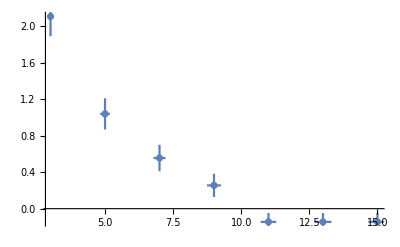

```mathematica
ErrorListPlot[Table[{PartBPlotData[[i]],ErrorBar[25.4*0.005*√i,PartBDeadTimeAndBackgroundCorrectedCountRateErrors[[i]]]},{i,Length[PartBPo210SourceDistance]}]]
```

```mathematica
PartABackgroundCountRate
```

0.645

3. Using equation 2, determine the range of alpha particles in air.

Equation 2, from the assignment:
R(mm)=(0.05T+2.85)T^(3/2),4<T<15 MeV
From https://www.nndc.bnl.gov/chart/decaysearchdirect.jsp?nuc=210PO&unc=nds, the energy of the alpha from Po-210 is 5304.33 keV

```mathematica
(0.05*5.30433+2.85)*5.30433^(3/2) (* mm *)
```

38.057

4. In a text-style cell, compare the calculated and experimentally determined answers. Comment on their level of agreement.

The calculated and experimental results do not agree at all. Overlooking the fact that the background-corrected counts go below zero (even accounting for error), the range appears to be around 10 mm rather than 38.057 mm, nearly a factor of four. This attenuation could be meaningful--possible causes include the shielding from the mica window integral to the detector, possible systematic error in the background count, or

```mathematica
Gamma-ray attenuation
```

Gamma-attenuation ray

1. From the data collected, determine the background and dead time corrected count rate, with uncertainty, for all absorbers (number them r_10, r_20, r_30, ...). Noting the amount counted with just a single aluminum shim, normalize the results. This represents the relative transmission.

2. From the data, estimate the mass attenuation coefficient using linear regression and its uncertainty. Report the value in a text-style cell.

```mathematica
TwoGammaAttenuation=a1*ⅇ^(-l1*t)+a2*ⅇ^(-l2*t)
```

a1 ⅇ^(-l1 t)+a2 ⅇ^(-l2 t)

2a. Graduate students: Calculate the mass attenuation coefficient including the weights of each datum.

3. Provide a semi-log plot of the data and the calculated fit as a function of mass thickness of the absorber.

4. Compare the mass attenuation coefficient experimentally calculated to the NIST value (text-style cell). Do the two agree? Is there an unaccounted for buildup factor? Quantify the discrepancy, if any.